## Input Data

```mathematica
f77Eform[x_?NumericQ,fw_Integer,ndig_Integer]:=Module[{sig,s,p,ps},{s,p}=MantissaExponent[x];
{sig,ps}={ToString[Round[10^ndig Abs[s]]],ToString[Abs[p]]};
StringJoin@@Join[Table[" ",{fw-ndig-7}],If[x<0,"-"," "],{"0."},{sig},Table["0",{ndig-StringLength[sig]}],{"E"},If[p<0,{"-"},{"+"}],Table["0",{2-StringLength[ps]}],{ps}]];

"0.010000	1.192163	-8.999842	-7.807679
0.060000	1.197171	-9.005060	-7.807888
0.110000	1.209305	-9.017693	-7.808388
0.160000	1.228489	-9.037648	-7.809158
0.210000	1.254609	-9.064777	-7.810167
0.260000	1.287508	-9.098880	-7.811372
0.310000	1.326985	-9.139704	-7.812718
0.360000	1.372806	-9.186948	-7.814142
0.410000	1.424697	-9.240264	-7.815568
0.460000	1.482347	-9.299260	-7.816913
0.510000	1.545417	-9.363503	-7.818085
0.560000	1.613536	-9.432522	-7.818986
0.610000	1.686305	-9.505813	-7.819508
0.660000	1.763302	-9.582842	-7.819539
0.710000	1.844085	-9.663049	-7.818964
0.760000	1.928192	-9.745852	-7.817661
0.810000	2.015147	-9.830653	-7.815506
0.860000	2.104466	-9.916840	-7.812375
0.910000	2.195653	-10.003792	-7.808140
0.960000	2.288209	-10.090884	-7.802675
1.010000	2.381634	-10.177489	-7.795855
1.060000	2.475430	-10.262984	-7.787554
1.110000	2.569103	-10.346755	-7.777652
1.160000	2.662166	-10.428196	-7.766030
1.210000	2.754145	-10.506717	-7.752572
1.260000	2.844576	-10.581743	-7.737167
1.310000	2.933011	-10.652722	-7.719711
1.360000	3.019020	-10.719121	-7.700101
1.410000	3.102190	-10.780434	-7.678244
1.460000	3.182133	-10.836181	-7.654049
1.510000	3.258478	-10.885911	-7.627434
1.560000	3.330881	-10.929202	-7.598322
1.610000	3.399021	-10.965665	-7.566644
1.660000	3.462604	-10.994940	-7.532336
1.710000	3.521361	-11.016704	-7.495343
1.760000	3.575049	-11.030665	-7.455616
1.810000	3.623454	-11.036568	-7.413114
1.860000	3.666387	-11.034189	-7.367801
1.910000	3.703689	-11.023341	-7.319652
1.960000	3.735226	-11.003872	-7.268646
2.010000	3.760893	-10.975665	-7.214772
2.060000	3.780610	-10.938635	-7.158025
2.110000	3.794327	-10.892736	-7.098409
2.160000	3.802018	-10.837953	-7.035935
2.210000	3.803684	-10.774304	-6.970620
2.260000	3.799351	-10.701843	-6.902492
2.310000	3.789070	-10.620655	-6.831585
2.360000	3.772917	-10.530857	-6.757940
2.410000	3.750992	-10.432598	-6.681606
2.460000	3.723415	-10.326056	-6.602641
2.510000	3.690330	-10.211439	-6.521110
2.560000	3.651901	-10.088984	-6.437083
2.610000	3.608314	-9.958954	-6.350640
2.660000	3.559769	-9.821637	-6.261868
2.710000	3.506487	-9.677346	-6.170859
2.760000	3.448704	-9.526417	-6.077713
2.810000	3.386670	-9.369206	-5.982535
2.860000	3.320649	-9.206086	-5.885438
2.910000	3.250913	-9.037451	-5.786538
2.960000	3.177750	-8.863706	-5.685956
3.010000	3.101450	-8.685271	-5.583821
3.060000	3.022313	-8.502574	-5.480261
3.110000	2.940642	-8.316054	-5.375412
3.160000	2.856744	-8.126153	-5.269409
3.210000	2.770926	-7.933319	-5.162393
3.260000	2.683495	-7.737999	-5.054504
3.310000	2.594756	-7.540639	-4.945883
3.360000	2.505009	-7.341683	-4.836674
3.410000	2.414549	-7.141568	-4.727019
3.460000	2.323665	-6.940723	-4.617059
3.510000	2.232635	-6.739570	-4.506935
3.560000	2.141730	-6.538516	-4.396786
3.610000	2.051209	-6.337957	-4.286748
3.660000	1.961318	-6.138273	-4.176956
3.710000	1.872291	-5.939829	-4.067538
3.760000	1.784348	-5.742972	-3.958623
3.810000	1.697696	-5.548030	-3.850334
3.860000	1.612524	-5.355312	-3.742788
3.910000	1.529009	-5.165109	-3.636100
3.960000	1.447310	-4.977688	-3.530378
4.010000	1.367571	-4.793298	-3.425727
4.060000	1.289920	-4.612166	-3.322246
4.110000	1.214471	-4.434498	-3.220027
4.160000	1.141319	-4.260477	-3.119158
4.210000	1.070548	-4.090269	-3.019721
4.260000	1.002224	-3.924017	-2.921793
4.310000	0.936400	-3.761844	-2.825444
4.360000	0.873117	-3.603856	-2.730739
4.410000	0.812400	-3.450137	-2.637737
4.460000	0.754263	-3.300756	-2.546493
4.510000	0.698710	-3.155767	-2.457057
4.560000	0.645730	-3.015201	-2.369471
4.610000	0.595306	-2.879079	-2.283773
4.660000	0.547411	-2.747404	-2.199994
4.710000	0.502007	-2.620167	-2.118160
4.760000	0.459051	-2.497345	-2.038294
4.810000	0.418492	-2.378904	-1.960412
4.860000	0.380272	-2.264800	-1.884528
4.910000	0.344330	-2.154979	-1.810649
4.960000	0.310600	-2.049379	-1.738779
5.010000	0.279009	-1.947927	-1.668918
5.060000	0.249484	-1.850547	-1.601062
5.110000	0.221949	-1.757154	-1.535204
5.160000	0.196326	-1.667658	-1.471333
5.210000	0.172534	-1.581967	-1.409433
5.260000	0.150492	-1.499982	-1.349489
5.310000	0.130121	-1.421601	-1.291480
5.360000	0.111339	-1.346722	-1.235382
5.410000	0.094066	-1.275238	-1.181172
5.460000	0.078223	-1.207043	-1.128821
5.510000	0.063730	-1.142029	-1.078299
5.560000	0.050512	-1.080088	-1.029576
5.610000	0.038493	-1.021112	-0.982618
5.660000	0.027601	-0.964992	-0.937391
5.710000	0.017764	-0.911623	-0.893858
5.760000	0.008915	-0.860898	-0.851983
5.810000	0.000986	-0.812713	-0.811727
5.860000	-0.006085	-0.766966	-0.773051
5.910000	-0.012360	-0.723555	-0.735916
5.960000	-0.017897	-0.682383	-0.700280
6.010000	-0.022752	-0.643353	-0.666105
6.060000	-0.026976	-0.606371	-0.633347
6.110000	-0.030622	-0.571345	-0.601967
6.160000	-0.033735	-0.538187	-0.571922
6.210000	-0.036362	-0.506810	-0.543172
6.260000	-0.038545	-0.477132	-0.515676
6.310000	-0.040322	-0.449071	-0.489393
6.360000	-0.041732	-0.422549	-0.464281
6.410000	-0.042810	-0.397492	-0.440302
6.460000	-0.043588	-0.373827	-0.417415
6.510000	-0.044096	-0.351485	-0.395582
6.560000	-0.044364	-0.330399	-0.374763
6.610000	-0.044416	-0.310505	-0.354921
6.660000	-0.044278	-0.291742	-0.336020
6.710000	-0.043972	-0.274050	-0.318022
6.760000	-0.043518	-0.257374	-0.300892
6.810000	-0.042936	-0.241659	-0.284595
6.860000	-0.042243	-0.226855	-0.269098
6.910000	-0.041454	-0.212913	-0.254367
6.960000	-0.040585	-0.199786	-0.240371
7.010000	-0.039649	-0.187429	-0.227078
7.060000	-0.038657	-0.175801	-0.214458
7.110000	-0.037620	-0.164860	-0.202481
7.160000	-0.036549	-0.154570	-0.191119
7.210000	-0.035451	-0.144893	-0.180344
7.260000	-0.034336	-0.135795	-0.170131
7.310000	-0.033209	-0.127243	-0.160452
7.360000	-0.032077	-0.119207	-0.151284
7.410000	-0.030946	-0.111657	-0.142603
7.460000	-0.029820	-0.104565	-0.134384
7.510000	-0.028703	-0.097905	-0.126608
7.560000	-0.027600	-0.091651	-0.119251
7.610000	-0.026513	-0.085780	-0.112294
7.660000	-0.025446	-0.080271	-0.105716
7.710000	-0.024399	-0.075101	-0.099500
7.760000	-0.023377	-0.070251	-0.093627
7.810000	-0.022379	-0.065701	-0.088080
7.860000	-0.021407	-0.061435	-0.082842
7.910000	-0.020463	-0.057435	-0.077897
7.960000	-0.019546	-0.053685	-0.073231
8.010000	-0.018658	-0.050171	-0.068829
8.060000	-0.017799	-0.046877	-0.064677
8.110000	-0.016970	-0.043791	-0.060761
8.160000	-0.016169	-0.040901	-0.057070
8.210000	-0.015397	-0.038194	-0.053591
8.260000	-0.014655	-0.035659	-0.050314
8.310000	-0.013941	-0.033285	-0.047226
8.360000	-0.013255	-0.031064	-0.044318
8.410000	-0.012597	-0.028984	-0.041580
8.460000	-0.011966	-0.027038	-0.039003
8.510000	-0.011361	-0.025217	-0.036578
8.560000	-0.010783	-0.023513	-0.034296
8.610000	-0.010230	-0.021919	-0.032149
8.660000	-0.009702	-0.020428	-0.030130
8.710000	-0.009198	-0.019034	-0.028232
8.760000	-0.008717	-0.017730	-0.026447
8.810000	-0.008258	-0.016512	-0.024770
8.860000	-0.007822	-0.015372	-0.023194
8.910000	-0.007406	-0.014307	-0.021713
8.960000	-0.007011	-0.013311	-0.020322
9.010000	-0.006635	-0.012381	-0.019016
9.060000	-0.006278	-0.011512	-0.017789
9.110000	-0.005939	-0.010699	-0.016638
9.160000	-0.005617	-0.009941	-0.015558
9.210000	-0.005311	-0.009232	-0.014544
9.260000	-0.005022	-0.008570	-0.013592
9.310000	-0.004747	-0.007953	-0.012700
9.360000	-0.004487	-0.007376	-0.011863
9.410000	-0.004241	-0.006838	-0.011079
9.460000	-0.004008	-0.006336	-0.010343
9.510000	-0.003787	-0.005867	-0.009654
9.560000	-0.003578	-0.005430	-0.009008
9.610000	-0.003380	-0.005023	-0.008403
9.660000	-0.003193	-0.004643	-0.007837
9.710000	-0.003017	-0.004289	-0.007306
9.760000	-0.002850	-0.003959	-0.006809
9.810000	-0.002692	-0.003652	-0.006344
9.860000	-0.002542	-0.003366	-0.005909
9.910000	-0.002402	-0.003100	-0.005501
9.960000	-0.002268	-0.002852	-0.005120
10.010000	-0.002143	-0.002622	-0.004764
";
ImportString[%,"Table"];
Drop[%,None,{2,3}];
ddn=%;
```

```mathematica
"0.010000	55.376352	-96.794760	-41.418408
0.060000	55.356398	-96.749680	-41.393283
0.110000	55.307682	-96.640064	-41.332381
0.160000	55.229576	-96.465570	-41.235994
0.210000	55.121096	-96.225670	-41.104574
0.260000	54.980927	-95.919664	-40.938737
0.310000	54.807451	-95.546696	-40.739245
0.360000	54.598790	-95.105788	-40.506998
0.410000	54.352840	-94.595863	-40.243023
0.460000	54.067327	-94.015783	-39.948456
0.510000	53.739859	-93.364386	-39.624527
0.560000	53.367981	-92.640526	-39.272545
0.610000	52.949235	-91.843116	-38.893880
0.660000	52.481224	-90.971168	-38.489945
0.710000	51.961665	-90.023843	-38.062178
0.760000	51.388456	-89.000487	-37.612030
0.810000	50.759732	-87.900678	-37.140946
0.860000	50.073914	-86.724264	-36.650350
0.910000	49.329767	-85.471402	-36.141635
0.960000	48.526437	-84.142588	-35.616151
1.010000	47.663494	-82.738688	-35.075194
1.060000	46.740965	-81.260964	-34.519999
1.110000	45.759353	-79.711093	-33.951740
1.160000	44.719661	-78.091177	-33.371516
1.210000	43.623396	-76.403756	-32.780360
1.260000	42.472572	-74.651805	-32.179233
1.310000	41.269704	-72.838731	-31.569028
1.360000	40.017789	-70.968362	-30.950574
1.410000	38.720288	-69.044929	-30.324641
1.460000	37.381097	-67.073041	-29.691945
1.510000	36.004504	-65.057660	-29.053156
1.560000	34.595157	-63.004063	-28.408906
1.610000	33.158010	-60.917805	-27.759795
1.660000	31.698274	-58.804677	-27.106403
1.710000	30.221363	-56.670657	-26.449294
1.760000	28.732839	-54.521865	-25.789026
1.810000	27.238350	-52.364508	-25.126159
1.860000	25.743575	-50.204834	-24.461259
1.910000	24.254165	-48.049071	-23.794906
1.960000	22.775685	-45.903384	-23.127698
2.010000	21.313563	-43.773818	-22.460255
2.060000	19.873034	-41.666254	-21.793220
2.110000	18.459095	-39.586356	-21.127261
2.160000	17.076463	-37.539537	-20.463074
2.210000	15.729533	-35.530910	-19.801376
2.260000	14.422347	-33.565257	-19.142910
2.310000	13.158564	-31.647000	-18.488437
2.360000	11.941440	-29.780172	-17.838732
2.410000	10.773811	-27.968395	-17.194584
2.460000	9.658082	-26.214867	-16.556785
2.510000	8.596219	-24.522349	-15.926130
2.560000	7.589755	-22.893161	-15.303406
2.610000	6.639791	-21.329180	-14.689389
2.660000	5.747009	-19.831845	-14.084836
2.710000	4.911685	-18.402166	-13.490481
2.760000	4.133708	-17.040736	-12.907028
2.810000	3.412603	-15.747747	-12.335145
2.860000	2.747554	-14.523015	-11.775461
2.910000	2.137436	-13.365996	-11.228560
2.960000	1.580838	-12.275816	-10.694978
3.010000	1.076098	-11.251298	-10.175200
3.060000	0.621333	-10.290991	-9.669658
3.110000	0.214471	-9.393199	-9.178727
3.160000	-0.146716	-8.556011	-8.702727
3.210000	-0.464584	-7.777335	-8.241918
3.260000	-0.741585	-7.054923	-7.796508
3.310000	-0.980237	-6.386407	-7.366645
3.360000	-1.183099	-5.769322	-6.952421
3.410000	-1.352745	-5.201134	-6.553879
3.460000	-1.491736	-4.679269	-6.171005
3.510000	-1.602607	-4.201133	-5.803740
3.560000	-1.687840	-3.764137	-5.451977
3.610000	-1.749850	-3.365714	-5.115564
3.660000	-1.790971	-3.003338	-4.794310
3.710000	-1.813444	-2.674540	-4.487984
3.760000	-1.819403	-2.376920	-4.196323
3.810000	-1.810870	-2.108161	-3.919031
3.860000	-1.789750	-1.866033	-3.655784
3.910000	-1.757824	-1.648409	-3.406232
3.960000	-1.716746	-1.453261	-3.170007
4.010000	-1.668046	-1.278671	-2.946717
4.060000	-1.613126	-1.122830	-2.735956
4.110000	-1.553267	-0.984039	-2.537307
4.160000	-1.489627	-0.860712	-2.350339
4.210000	-1.423245	-0.751371	-2.174616
4.260000	-1.355051	-0.654643	-2.009694
4.310000	-1.285867	-0.569262	-1.855129
4.360000	-1.216411	-0.494063	-1.710473
4.410000	-1.147309	-0.427973	-1.575281
4.460000	-1.079096	-0.370015	-1.449111
4.510000	-1.012226	-0.319296	-1.331522
4.560000	-0.947078	-0.275007	-1.222085
4.610000	-0.883960	-0.236414	-1.120373
4.660000	-0.823118	-0.202854	-1.025972
4.710000	-0.764743	-0.173731	-0.938475
4.760000	-0.708975	-0.148512	-0.857487
4.810000	-0.655908	-0.126717	-0.782625
4.860000	-0.605599	-0.107920	-0.713519
4.910000	-0.558070	-0.091741	-0.649810
4.960000	-0.513312	-0.077843	-0.591155
5.010000	-0.471295	-0.065929	-0.537223
5.060000	-0.431964	-0.055735	-0.487699
5.110000	-0.395249	-0.047031	-0.442280
5.160000	-0.361067	-0.039613	-0.400679
5.210000	-0.329321	-0.033303	-0.362623
5.260000	-0.299908	-0.027947	-0.327854
5.310000	-0.272718	-0.023408	-0.296126
5.360000	-0.247639	-0.019570	-0.267209
5.410000	-0.224555	-0.016330	-0.240886
5.460000	-0.203350	-0.013601	-0.216951
5.510000	-0.183907	-0.011306	-0.195213
5.560000	-0.166114	-0.009380	-0.175494
5.610000	-0.149860	-0.007766	-0.157626
5.660000	-0.135037	-0.006417	-0.141453
5.710000	-0.121540	-0.005291	-0.126831
5.760000	-0.109272	-0.004352	-0.113625
5.810000	-0.098137	-0.003572	-0.101710
5.860000	-0.088046	-0.002925	-0.090971
5.910000	-0.078913	-0.002388	-0.081301
5.960000	-0.070660	-0.001944	-0.072604
6.010000	-0.063210	-0.001578	-0.064788
6.060000	-0.056495	-0.001276	-0.057771
6.110000	-0.050450	-0.001028	-0.051478
6.160000	-0.045014	-0.000824	-0.045838
6.210000	-0.040131	-0.000657	-0.040788
6.260000	-0.035750	-0.000520	-0.036270
6.310000	-0.031824	-0.000408	-0.032232
6.360000	-0.028308	-0.000317	-0.028626
6.410000	-0.025164	-0.000243	-0.025407
6.460000	-0.022354	-0.000183	-0.022537
6.510000	-0.019845	-0.000135	-0.019980
6.560000	-0.017608	-0.000095	-0.017703
6.610000	-0.015613	-0.000063	-0.015677
6.660000	-0.013837	-0.000038	-0.013875
6.710000	-0.012256	-0.000017	-0.012274
6.760000	-0.010851	-0.000001	-0.010852
6.810000	-0.009602	0.000012	-0.009590
6.860000	-0.008493	0.000023	-0.008470
6.910000	-0.007510	0.000031	-0.007478
6.960000	-0.006637	0.000038	-0.006599
7.010000	-0.005864	0.000043	-0.005820
7.060000	-0.005179	0.000047	-0.005131
7.110000	-0.004572	0.000051	-0.004522
7.160000	-0.004035	0.000053	-0.003982
7.210000	-0.003561	0.000055	-0.003506
7.260000	-0.003141	0.000056	-0.003085
7.310000	-0.002771	0.000058	-0.002713
7.360000	-0.002443	0.000058	-0.002385
7.410000	-0.002154	0.000059	-0.002095
7.460000	-0.001899	0.000059	-0.001840
7.510000	-0.001674	0.000060	-0.001614
7.560000	-0.001475	0.000060	-0.001416
7.610000	-0.001301	0.000060	-0.001241
7.660000	-0.001146	0.000060	-0.001087
7.710000	-0.001010	0.000060	-0.000951
7.760000	-0.000891	0.000059	-0.000831
7.810000	-0.000785	0.000059	-0.000726
7.860000	-0.000692	0.000059	-0.000633
7.910000	-0.000611	0.000059	-0.000552
7.960000	-0.000539	0.000059	-0.000480
8.010000	-0.000475	0.000058	-0.000417
8.060000	-0.000420	0.000058	-0.000362
8.110000	-0.000371	0.000058	-0.000313
8.160000	-0.000328	0.000058	-0.000270
8.210000	-0.000290	0.000057	-0.000232
8.260000	-0.000256	0.000057	-0.000199
8.310000	-0.000227	0.000057	-0.000170
8.360000	-0.000201	0.000056	-0.000145
8.410000	-0.000179	0.000056	-0.000123
8.460000	-0.000159	0.000056	-0.000103
8.510000	-0.000141	0.000055	-0.000086
8.560000	-0.000126	0.000055	-0.000071
8.610000	-0.000112	0.000055	-0.000058
8.660000	-0.000100	0.000054	-0.000046
8.710000	-0.000090	0.000054	-0.000036
8.760000	-0.000081	0.000054	-0.000027
8.810000	-0.000073	0.000053	-0.000019
8.860000	-0.000066	0.000053	-0.000012
8.910000	-0.000059	0.000053	-0.000006
8.960000	-0.000054	0.000052	-0.000001
9.010000	-0.000049	0.000052	0.000003
9.060000	-0.000045	0.000052	0.000007
9.110000	-0.000041	0.000051	0.000011
9.160000	-0.000038	0.000051	0.000014
9.210000	-0.000035	0.000051	0.000016
9.260000	-0.000032	0.000050	0.000018
9.310000	-0.000030	0.000050	0.000020
9.360000	-0.000028	0.000050	0.000022
9.410000	-0.000026	0.000049	0.000023
9.460000	-0.000024	0.000049	0.000025
9.510000	-0.000023	0.000049	0.000026
9.560000	-0.000022	0.000048	0.000026
9.610000	-0.000021	0.000048	0.000027
9.660000	-0.000020	0.000048	0.000028
9.710000	-0.000019	0.000047	0.000028
9.760000	-0.000018	0.000047	0.000029
9.810000	-0.000017	0.000046	0.000029
9.860000	-0.000017	0.000046	0.000029
9.910000	-0.000016	0.000046	0.000029
9.960000	-0.000016	0.000045	0.000030
10.010000	-0.000015	0.000045	0.000030
";
ImportString[%,"Table"];
Drop[%,None,{2,3}];
dda=%;
```

```mathematica
"9.4964E+00  1.0144E+03  0.0000E+00   0.0000E+00
 1.1655E+01  2.7213E+02  0.0000E+00   0.0000E+00
 1.4676E+01  6.5113E+01  0.0000E+00   0.0000E+00
 1.7660E+01  8.4298E+01  0.0000E+00   0.0000E+00
 2.1463E+01  6.0973E+01  0.0000E+00   0.0000E+00
 2.6894E+01  3.3068E+01  0.0000E+00   0.0000E+00
 2.9882E+01  1.0083E+01  0.0000E+00   0.0000E+00
 3.3684E+01  5.2749E+00  0.0000E+00   0.0000E+00
 3.7758E+01  3.0743E+00  0.0000E+00   0.0000E+00
 4.1288E+01  1.6084E+00  0.0000E+00   0.0000E+00
 4.4547E+01  1.0443E+00  0.0000E+00   0.0000E+00
 4.9708E+01  3.1840E-01  0.0000E+00   0.0000E+00
 5.3510E+01  2.2216E-01  0.0000E+00   0.0000E+00
 5.7312E+01  4.0926E-02  0.0000E+00   0.0000E+00
 6.1386E+01  3.6737E-02  0.0000E+00   0.0000E+00
 6.5188E+01  9.6996E-03  3.2365E-03  -3.4019E-03
 6.9262E+01  8.1021E-03  3.0994E-03  -3.0276E-03
 7.3335E+01  4.2387E-03  2.0589E-03  -2.0212E-03
 7.7138E+01  6.5284E-03  2.4974E-03  -2.1344E-03
 8.0668E+01  2.5609E-03  1.3834E-03  -1.2211E-03
 1.0946E+02  3.8014E-04  2.2680E-04  -2.0793E-04
 1.1462E+02  1.3889E-03  5.3132E-04  -5.4975E-04
 1.1950E+02  1.5472E-03  1.0137E-03  -7.3778E-04
 1.2466E+02  6.2976E-03  0.0000E+00   0.0000E+00
 1.2983E+02  6.7677E-03  0.0000E+00   0.0000E+00
 1.3444E+02  1.5487E-02  0.0000E+00   0.0000E+00
 1.3960E+02  1.3410E-02  0.0000E+00   0.0000E+00
 1.4476E+02  2.9602E-02  0.0000E+00   0.0000E+00
 1.4965E+02  5.4582E-02  0.0000E+00   0.0000E+00
 1.5372E+02  5.0791E-02  0.0000E+00   0.0000E+00
 1.5943E+02  1.3410E-02  0.0000E+00   0.0000E+00
 1.6486E+02  4.5593E-02  0.0000E+00   0.0000E+00
 1.6893E+02  8.7148E-02  0.0000E+00   0.0000E+00
 1.7491E+02  1.1623E-01  3.8782E-02  -3.5132E-02";
expScatData=ImportString[%,"Table"];
```

```mathematica
"4.0	 	2419.04052729
5.0	 	2079.11276404
6.0	 	1870.49126795
7.0	 	1613.97137254
8.0	 	1325.185296
9.0	 	1038.19022314
10.0	 	778.588753803
11.0	 	560.241216973
12.0	 	387.903011574
13.0	 	259.795372659
14.0	 	170.137957628
15.0	 	111.325448451
16.0	 	75.4842425063
17.0	 	55.4931126848
18.0	 	45.5195498302
19.0	 	41.1835568758
20.0	 	39.4737307226
21.0	 	38.5162366156
22.0	 	37.3035229952
23.0	 	35.4153048943
24.0	 	32.8075792688
25.0	 	29.6341260169
26.0	 	26.1304318936
27.0	 	22.5405092686
28.0	 	19.0712026929
29.0	 	15.8758280321
30.0	 	13.0498968344
31.0	 	10.6366120374
32.0	 	8.63551030685
33.0	 	7.01644662876
34.0	 	5.73100357819
35.0	 	4.72191947846
36.0	 	3.93331118158
37.0	 	3.31465463642
38.0	 	2.82354313456
39.0	 	2.42651010832
40.0	 	2.09861793116
41.0	 	1.82168563966
42.0	 	1.58301789202
43.0	 	1.37377055693
44.0	 	1.18797914814
45.0	 	1.02180198076
46.0	 	0.872776129935
47.0	 	0.739508207503
48.0	 	0.621272936635
49.0	 	0.51761968132
50.0	 	0.428136822797
51.0	 	0.352220518522
52.0	 	0.288935166046
53.0	 	0.237019158999
54.0	 	0.194967956401
55.0	 	0.161143743652
56.0	 	0.133981557838
57.0	 	0.112046869464
58.0	 	0.0941598137846
59.0	 	0.0794032876414
60.0	 	0.067103615303
61.0	 	0.0567779439812
62.0	 	0.0480863391218
63.0	 	0.0407515415049
64.0	 	0.0345711714735
65.0	 	0.0293461431281
66.0	 	0.0249063685115
67.0	 	0.0211046915352
68.0	 	0.0178223859254
69.0	 	0.0149731973336
70.0	 	0.0124988664767
71.0	 	0.010363771759
72.0	 	0.00854469644043
73.0	 	0.00702261909826
74.0	 	0.00577485873507
75.0	 	0.00477235702564
76.0	 	0.00397825994044
77.0	 	0.00335240639037
78.0	 	0.0028541011637
79.0	 	0.00244773224096
80.0	 	0.00210472423467
81.0	 	0.00180579346831
82.0	 	0.0015399055485
83.0	 	0.0013026240668
84.0	 	0.00109324895947
85.0	 	0.000912623604552
86.0	 	0.000760832438701
87.0	 	0.00063655477782
88.0	 	0.000536743626585
89.0	 	0.000457138052936
90.0	 	0.000393080698154
91.0	 	0.000340479091372
92.0	 	0.000296241060818
93.0	 	0.000258593776161
94.0	 	0.00022697206075
95.0	 	0.000201674146464
96.0	 	0.000183413188608
97.0	 	0.000172869236349
98.0	 	0.00017037614612
99.0	 	0.000175739056202
100.0	 	0.000188269995471
101.0	 	0.000206931447746
102.0	 	0.000230608007142
103.0	 	0.000258398363987
104.0	 	0.000289875534475
105.0	 	0.000325251963574
106.0	 	0.000365404809109
107.0	 	0.00041176470768
108.0	 	0.000466050324109
109.0	 	0.000529986322402
110.0	 	0.000604934641183
111.0	 	0.000691699894764
112.0	 	0.00079038176325
113.0	 	0.000900605001369
114.0	 	0.00102154475514
115.0	 	0.00115270315159
116.0	 	0.00129399400376
117.0	 	0.00144664252247
118.0	 	0.00161306226927
119.0	 	0.0017974299535
120.0	 	0.00200543314326
121.0	 	0.00224410993123
122.0	 	0.00252160182144
123.0	 	0.00284645651059
124.0	 	0.00322724352741
125.0	 	0.00367181053654
126.0	 	0.00418663226885
127.0	 	0.00477628904059
128.0	 	0.00544349250991
129.0	 	0.00618882524811
130.0	 	0.00701173926167
131.0	 	0.00791091130706
132.0	 	0.00888765407953
133.0	 	0.00994498429864
134.0	 	0.011091332112
135.0	 	0.0123399796836
136.0	 	0.0137092555538
137.0	 	0.0152201996361
138.0	 	0.0168924409436
139.0	 	0.0187422336403
140.0	 	0.0207763329946
141.0	 	0.0229879720518
142.0	 	0.0253571937543
143.0	 	0.0278513828113
144.0	 	0.0304260598531
145.0	 	0.0330338187342
146.0	 	0.0356289312687
147.0	 	0.0381743337256
148.0	 	0.0406484047954
149.0	 	0.043048939348
150.0	 	0.0453925697109
151.0	 	0.0477153649819
152.0	 	0.0500677251372
153.0	 	0.0525102386853
154.0	 	0.0551114108934
155.0	 	0.0579428585692
156.0	 	0.0610783751921
157.0	 	0.0645991285615
158.0	 	0.0685897717206
159.0	 	0.0731545318654
160.0	 	0.0784159285278
161.0	 	0.0845235171013
162.0	 	0.0916451332814
163.0	 	0.0999717490331
164.0	 	0.109698467566
165.0	 	0.121020280618
166.0	 	0.134079091227
167.0	 	0.148972401687
168.0	 	0.165687543044
169.0	 	0.184108376561
170.0	 	0.203979525298
171.0	 	0.224913357768
172.0	 	0.246381619585
173.0	 	0.267755136542
174.0	 	0.288332152116
175.0	 	0.307375095435
176.0	 	0.324151393412";
cs0=ImportString[%,"Table"];
```

```mathematica
"4.0	 	2419.0405269
5.0	 	2079.11276366
6.0	 	1870.49126756
7.0	 	1613.97137216
8.0	 	1325.18529561
9.0	 	1038.19022276
10.0	 	778.588753426
11.0	 	560.241216602
12.0	 	387.903011211
13.0	 	259.795372305
14.0	 	170.137957289
15.0	 	111.325448129
16.0	 	75.4842422043
17.0	 	55.4931124063
18.0	 	45.5195495776
19.0	 	41.1835566505
20.0	 	39.4737305247
21.0	 	38.5162364438
22.0	 	37.3035228462
23.0	 	35.4153047633
24.0	 	32.8075791492
25.0	 	29.6341259011
26.0	 	26.1304317729
27.0	 	22.5405091341
28.0	 	19.0712025364
29.0	 	15.8758278466
30.0	 	13.0498966148
31.0	 	10.6366117816
32.0	 	8.6355100158
33.0	 	7.0164463067
34.0	 	5.73100323248
35.0	 	4.72191911893
36.0	 	3.93331081957
37.0	 	3.31465428334
38.0	 	2.82354280039
39.0	 	2.42650979989
40.0	 	2.09861765063
41.0	 	1.82168538332
42.0	 	1.58301764974
43.0	 	1.37377031222
44.0	 	1.18797887924
45.0	 	1.02180166256
46.0	 	0.872775736631
47.0	 	0.739507715818
48.0	 	0.621272329154
49.0	 	0.517618949424
50.0	 	0.428135968873
51.0	 	0.352219556673
52.0	 	0.288934121109
53.0	 	0.237018063807
54.0	 	0.194966847252
55.0	 	0.161142654455
56.0	 	0.133980513822
57.0	 	0.112045881029
58.0	 	0.094158872114
59.0	 	0.0794023625149
60.0	 	0.0671026560129
61.0	 	0.0567768836727
62.0	 	0.0480851021042
63.0	 	0.0407500527794
64.0	 	0.034569366781
65.0	 	0.0293439780832
66.0	 	0.0249038248385
67.0	 	0.0211017790363
68.0	 	0.0178191394967
69.0	 	0.0149696692085
70.0	 	0.0124951144953
71.0	 	0.0103598462846
72.0	 	0.00854062767019
73.0	 	0.0070184073908
74.0	 	0.00577046992967
75.0	 	0.0047677232429
76.0	 	0.00397328491659
77.0	 	0.00334697406783
78.0	 	0.00284808477509
79.0	 	0.0024410010145
80.0	 	0.00209714608832
81.0	 	0.00179723294859
82.0	 	0.00153021881719
83.0	 	0.00129165220482
84.0	 	0.00108081283421
85.0	 	0.000898523750175
86.0	 	0.000744849649815
87.0	 	0.000618448444421
88.0	 	0.000516247817475
89.0	 	0.000433938082855
90.0	 	0.000366770495071
91.0	 	0.000310495760436
92.0	 	0.000261781642896
93.0	 	0.000218528270449
94.0	 	0.000179772224607
95.0	 	0.000145383464859
96.0	 	0.000115671001955
97.0	 	9.10018464079e-05
98.0	 	7.15339578698e-05
99.0	 	5.70652148197e-05
100.0	 	4.70268044317e-05
101.0	 	4.05642577178e-05
102.0	 	3.66716635484e-05
103.0	 	3.43470671914e-05
104.0	 	3.27096405624e-05
105.0	 	3.10951759133e-05
106.0	 	2.90937436535e-05
107.0	 	2.65374976439e-05
108.0	 	2.34682460528e-05
109.0	 	2.00676299378e-05
110.0	 	1.65920673138e-05
111.0	 	1.33060903265e-05
112.0	 	1.04234282562e-05
113.0	 	8.08497795681e-06
114.0	 	6.33830685246e-06
115.0	 	5.1461062046e-06
116.0	 	4.40855556858e-06
117.0	 	3.98892791725e-06
118.0	 	3.74391979501e-06
119.0	 	3.54843104598e-06
120.0	 	3.31306052354e-06
121.0	 	2.99148967481e-06
122.0	 	2.57936952009e-06
123.0	 	2.10547847335e-06
124.0	 	1.61876022274e-06
125.0	 	1.17424250342e-06
126.0	 	8.20419743881e-07
127.0	 	5.89932082669e-07
128.0	 	4.94998491053e-07
129.0	 	5.27103395422e-07
130.0	 	6.60429872824e-07
131.0	 	8.57790965939e-07
132.0	 	1.07752546305e-06
133.0	 	1.2801226e-06
134.0	 	1.43338940902e-06
135.0	 	1.51616701877e-06
136.0	 	1.51926916252e-06
137.0	 	1.44517442366e-06
138.0	 	1.3057795525e-06
139.0	 	1.11951982886e-06
140.0	 	9.07991222602e-07
141.0	 	6.92873371061e-07
142.0	 	4.93222611931e-07
143.0	 	3.23960926475e-07
144.0	 	1.94664621153e-07
145.0	 	1.09582725563e-07
146.0	 	6.80949103312e-08
147.0	 	6.563630886e-08
148.0	 	9.48796757388e-08
149.0	 	1.46954143256e-07
150.0	 	2.1259735798e-07
151.0	 	2.83015263567e-07
152.0	 	3.50587818226e-07
153.0	 	4.09259130897e-07
154.0	 	4.54771827183e-07
155.0	 	4.84527777641e-07
156.0	 	4.975657184e-07
157.0	 	4.94256822338e-07
158.0	 	4.76067906322e-07
159.0	 	4.45205213145e-07
160.0	 	4.04515861857e-07
161.0	 	3.57079447672e-07
162.0	 	3.06205030318e-07
163.0	 	2.55083336637e-07
164.0	 	2.06762441185e-07
165.0	 	1.64003162965e-07
166.0	 	1.29113483074e-07
167.0	 	1.03912714085e-07
168.0	 	8.95604401342e-08
169.0	 	8.65656878469e-08
170.0	 	9.47168520726e-08
171.0	 	1.13078943155e-07
172.0	 	1.40068593292e-07
173.0	 	1.73500324296e-07
174.0	 	2.10788495803e-07
175.0	 	2.49044435145e-07
176.0	 	2.85370117352e-07";
cs1=ImportString[%,"Table"];
```

```mathematica
"4.0	 	2.85007158029e-07
5.0	 	2.88312034371e-07
6.0	 	2.91901794734e-07
7.0	 	2.95467955306e-07
8.0	 	2.98589951321e-07
9.0	 	3.00766040704e-07
10.0	 	3.01440940865e-07
11.0	 	3.00001009503e-07
12.0	 	2.95840619125e-07
13.0	 	2.88436941542e-07
14.0	 	2.773446064e-07
15.0	 	2.62344462759e-07
16.0	 	2.43456879709e-07
17.0	 	2.20999725642e-07
18.0	 	1.95655184672e-07
19.0	 	1.68419942797e-07
20.0	 	1.40639011598e-07
21.0	 	1.13913337935e-07
22.0	 	9.00129718664e-08
23.0	 	7.07356806125e-08
24.0	 	5.77687622181e-08
25.0	 	5.24900113286e-08
26.0	 	5.58218490947e-08
27.0	 	6.80527263868e-08
28.0	 	8.87258415642e-08
29.0	 	1.16584868128e-07
30.0	 	1.49604986412e-07
31.0	 	1.85057626564e-07
32.0	 	2.19763159455e-07
33.0	 	2.5035918074e-07
34.0	 	2.73670299053e-07
35.0	 	2.87083610589e-07
36.0	 	2.88986508819e-07
37.0	 	2.79159185917e-07
38.0	 	2.58891526503e-07
39.0	 	2.31237802865e-07
40.0	 	2.00723409561e-07
41.0	 	1.73162273689e-07
42.0	 	1.54960877657e-07
43.0	 	1.52453456014e-07
44.0	 	1.70925742948e-07
45.0	 	2.13785044643e-07
46.0	 	2.81762632723e-07
47.0	 	3.72374911102e-07
48.0	 	4.79760542452e-07
49.0	 	5.95094204461e-07
50.0	 	7.072923144e-07
51.0	 	8.04496736976e-07
52.0	 	8.75739997115e-07
53.0	 	9.12797952524e-07
54.0	 	9.11854324818e-07
55.0	 	8.74945733899e-07
56.0	 	8.10380640507e-07
57.0	 	7.32565423304e-07
58.0	 	6.60367880774e-07
59.0	 	6.1481966195e-07
60.0	 	6.16075337539e-07
61.0	 	6.79993384906e-07
62.0	 	8.15168647105e-07
63.0	 	1.0206742371e-06
64.0	 	1.28552586075e-06
65.0	 	1.58965664934e-06
66.0	 	1.90669021515e-06
67.0	 	2.20824106674e-06
68.0	 	2.46884987147e-06
69.0	 	2.67072333603e-06
70.0	 	2.8075859175e-06
71.0	 	2.88626009102e-06
72.0	 	2.92594894156e-06
73.0	 	2.95548916768e-06
74.0	 	3.00809623223e-06
75.0	 	3.11615109341e-06
76.0	 	3.3063888758e-06
77.0	 	3.59668836645e-06
78.0	 	3.9958184225e-06
79.0	 	4.50543224087e-06
80.0	 	5.12431241078e-06
81.0	 	5.85295917375e-06
82.0	 	6.69659317656e-06
83.0	 	7.66669842961e-06
84.0	 	8.77953296511e-06
85.0	 	1.00509775484e-05
86.0	 	1.14957817107e-05
87.0	 	1.31297983116e-05
88.0	 	1.49719971305e-05
89.0	 	1.70642028826e-05
90.0	 	1.94897637225e-05
91.0	 	2.23972441792e-05
92.0	 	2.60166082301e-05
93.0	 	3.0663727734e-05
94.0	 	3.67235709733e-05
95.0	 	4.46115427088e-05
96.0	 	5.47138439469e-05
97.0	 	6.73253540664e-05
98.0	 	8.25999407476e-05
99.0	 	0.000100522006509
100.0	 	0.000120944305399
101.0	 	0.000143653422605
102.0	 	0.000168506202526
103.0	 	0.000195569728455
104.0	 	0.000225259493664
105.0	 	0.00025841164533
106.0	 	0.000296276784205
107.0	 	0.000340409114153
108.0	 	0.000392446942996
109.0	 	0.000453890546273
110.0	 	0.000525799066
111.0	 	0.000608666630162
112.0	 	0.0007023319943
113.0	 	0.000806213680258
114.0	 	0.000919372028712
115.0	 	0.00104126946361
116.0	 	0.00117182269276
117.0	 	0.00131228311626
118.0	 	0.00146507790391
119.0	 	0.0016343622464
120.0	 	0.00182574504078
121.0	 	0.00204612894782
122.0	 	0.00230346731503
123.0	 	0.00260606771908
124.0	 	0.0029622459544
125.0	 	0.00337958228562
126.0	 	0.0038643143871
127.0	 	0.00442081908948
128.0	 	0.00505166228512
129.0	 	0.00575734136836
130.0	 	0.0065373029964
131.0	 	0.00739028453285
132.0	 	0.0083177185654
133.0	 	0.00932279326537
134.0	 	0.0104141278251
135.0	 	0.0116051865458
136.0	 	0.0129144510003
137.0	 	0.0143629437544
138.0	 	0.0159703618152
139.0	 	0.0177526612419
140.0	 	0.0197162114969
141.0	 	0.021853864805
142.0	 	0.0241449832725
143.0	 	0.02655627833
144.0	 	0.0290427412125
145.0	 	0.0315564001418
146.0	 	0.0340512851012
147.0	 	0.0364903724613
148.0	 	0.0388524833307
149.0	 	0.0411363525486
150.0	 	0.0433598994643
151.0	 	0.0455609079294
152.0	 	0.04779153155
153.0	 	0.0501143807738
154.0	 	0.0525997285168
155.0	 	0.055320608296
156.0	 	0.0583513992482
157.0	 	0.0617734052074
158.0	 	0.0656698866412
159.0	 	0.0701427482462
160.0	 	0.0753111253963
161.0	 	0.0813199687
162.0	 	0.0883314725888
163.0	 	0.0965301784827
164.0	 	0.106104639805
165.0	 	0.117242959463
166.0	 	0.130081014609
167.0	 	0.144710982968
168.0	 	0.161117360541
169.0	 	0.179183029675
170.0	 	0.198655188394
171.0	 	0.21915196058
172.0	 	0.240155124383
173.0	 	0.2610493941
174.0	 	0.281150280313
175.0	 	0.29974002695
176.0	 	0.316107258187
";
cs2=ImportString[%,"Table"];
```

```mathematica
"4.0	 	1.00124124427e-07
5.0	 	9.65270592532e-08
6.0	 	9.24772081649e-08
7.0	 	8.81611024876e-08
8.0	 	8.37376136437e-08
9.0	 	7.9364146481e-08
10.0	 	7.51788414771e-08
11.0	 	7.12911311841e-08
12.0	 	6.77904278116e-08
13.0	 	6.47394934509e-08
14.0	 	6.21749535805e-08
15.0	 	6.01213362511e-08
16.0	 	5.85807360775e-08
17.0	 	5.7545290915e-08
18.0	 	5.69970722598e-08
19.0	 	5.69085639622e-08
20.0	 	5.72434097905e-08
21.0	 	5.79552534598e-08
22.0	 	5.89822746131e-08
23.0	 	6.02714234259e-08
24.0	 	6.17351080842e-08
25.0	 	6.33020408683e-08
26.0	 	6.48880259431e-08
27.0	 	6.64121566732e-08
28.0	 	6.77976667703e-08
29.0	 	6.90035220971e-08
30.0	 	6.99831888051e-08
31.0	 	7.07404968476e-08
32.0	 	7.12908686837e-08
33.0	 	7.1697902801e-08
34.0	 	7.20435957471e-08
35.0	 	7.244319504e-08
36.0	 	7.30214081862e-08
37.0	 	7.39172446233e-08
38.0	 	7.5270539446e-08
39.0	 	7.71997887273e-08
40.0	 	7.98081791249e-08
41.0	 	8.31697029495e-08
42.0	 	8.73200075189e-08
43.0	 	9.2256340725e-08
44.0	 	9.7976730636e-08
45.0	 	1.04412414003e-07
46.0	 	1.11541305791e-07
47.0	 	1.19310068794e-07
48.0	 	1.27720609025e-07
49.0	 	1.36801056757e-07
50.0	 	1.46631212651e-07
51.0	 	1.57352472494e-07
52.0	 	1.69197089411e-07
53.0	 	1.82394529499e-07
54.0	 	1.97295454596e-07
55.0	 	2.14251658463e-07
56.0	 	2.33635777636e-07
57.0	 	2.55870546411e-07
58.0	 	2.81302725754e-07
59.0	 	3.10306822202e-07
60.0	 	3.43214787924e-07
61.0	 	3.80315119973e-07
62.0	 	4.21848982659e-07
63.0	 	4.68051254474e-07
64.0	 	5.1916661314e-07
65.0	 	5.75388327199e-07
66.0	 	6.36982765958e-07
67.0	 	7.04257822768e-07
68.0	 	7.77578880418e-07
69.0	 	8.5740174048e-07
70.0	 	9.4439542304e-07
71.0	 	1.0392143073e-06
72.0	 	1.14282129728e-06
73.0	 	1.25621829761e-06
74.0	 	1.38070916462e-06
75.0	 	1.51763164802e-06
76.0	 	1.66863498241e-06
77.0	 	1.83563418153e-06
78.0	 	2.02057018905e-06
79.0	 	2.22579421989e-06
80.0	 	2.45383393951e-06
81.0	 	2.70756054214e-06
82.0	 	2.99013813129e-06
83.0	 	3.30516355149e-06
84.0	 	3.65659228907e-06
85.0	 	4.04887682856e-06
86.0	 	4.4870071754e-06
87.0	 	4.97653508726e-06
88.0	 	5.5238119795e-06
89.0	 	6.13576719865e-06
90.0	 	6.82043936041e-06
91.0	 	7.58608675625e-06
92.0	 	8.44280969187e-06
93.0	 	9.4017779786e-06
94.0	 	1.04762651691e-05
95.0	 	1.16791388957e-05
96.0	 	1.30283427063e-05
97.0	 	1.45420358752e-05
98.0	 	1.62422475028e-05
99.0	 	1.81518348735e-05
100.0	 	2.02988856407e-05
101.0	 	2.27137674239e-05
102.0	 	2.54301410669e-05
103.0	 	2.84815683403e-05
104.0	 	3.19064002484e-05
105.0	 	3.57451423304e-05
106.0	 	4.00342812502e-05
107.0	 	4.48180958834e-05
108.0	 	5.013513506e-05
109.0	 	5.60281461919e-05
110.0	 	6.25435078695e-05
111.0	 	6.9727174275e-05
112.0	 	7.76263406942e-05
113.0	 	8.63063431535e-05
114.0	 	9.58344195761e-05
115.0	 	0.00010628758178
116.0	 	0.000117762755426
117.0	 	0.000130370478291
118.0	 	0.000144240445569
119.0	 	0.000159519276052
120.0	 	0.000176375041958
121.0	 	0.00019498949373
122.0	 	0.00021555513689
123.0	 	0.000238283313038
124.0	 	0.000263378812789
125.0	 	0.000291054008411
126.0	 	0.000321497462002
127.0	 	0.000354880019031
128.0	 	0.0003913352263
129.0	 	0.00043095677635
130.0	 	0.0004737758354
131.0	 	0.000519768983241
132.0	 	0.000568857988663
133.0	 	0.000620910910668
134.0	 	0.000675770897512
135.0	 	0.000733276970863
136.0	 	0.000793285284313
137.0	 	0.000855810707296
138.0	 	0.00092077334881
139.0	 	0.000988452878638
140.0	 	0.00105921350649
141.0	 	0.00113341437345
142.0	 	0.00121171725921
143.0	 	0.0012947805204
144.0	 	0.001383123976
145.0	 	0.00147730900969
146.0	 	0.0015775780726
147.0	 	0.00168389562793
148.0	 	0.00179582658502
149.0	 	0.00191243984523
150.0	 	0.00203245764928
151.0	 	0.00215417403723
152.0	 	0.00227584299937
153.0	 	0.00239544865241
154.0	 	0.00251122760477
155.0	 	0.00262176574541
156.0	 	0.00272647837814
157.0	 	0.00282522909735
158.0	 	0.00291940901141
159.0	 	0.00301133841391
160.0	 	0.00310439861565
161.0	 	0.00320319132189
162.0	 	0.00331335448765
163.0	 	0.00344131546708
164.0	 	0.00359362099803
165.0	 	0.00377715715192
166.0	 	0.00399794750442
167.0	 	0.00426131480722
168.0	 	0.00457009294193
169.0	 	0.00492526031952
170.0	 	0.00532424218785
171.0	 	0.0057612841092
172.0	 	0.00622635513407
173.0	 	0.00670556894218
174.0	 	0.00718166101456
175.0	 	0.00763481944038
176.0	 	0.00804384985445
";
cs3=ImportString[%,"Table"];
```

```mathematica
"0.010000	63.456006	-125.352380	-61.896375
0.060000	63.448594	-125.316671	-61.868078
0.110000	63.430318	-125.229763	-61.799444
0.160000	63.400492	-125.091188	-61.690696
0.210000	63.358041	-124.900218	-61.542177
0.260000	63.301511	-124.655871	-61.354360
0.310000	63.229102	-124.356932	-61.127830
0.360000	63.138687	-124.001974	-60.863287
0.410000	63.027848	-123.589381	-60.561533
0.460000	62.893915	-123.117382	-60.223467
0.510000	62.734005	-122.584079	-59.850075
0.560000	62.545069	-121.987485	-59.442416
0.610000	62.323940	-121.325559	-59.001619
0.660000	62.067381	-120.596248	-58.528867
0.710000	61.772136	-119.797522	-58.025386
0.760000	61.434984	-118.927422	-57.492438
0.810000	61.052788	-117.984094	-56.931307
0.860000	60.622547	-116.965834	-56.343287
0.910000	60.141446	-115.871124	-55.729679
0.960000	59.606899	-114.698673	-55.091774
1.010000	59.016600	-113.447448	-54.430848
1.060000	58.368553	-112.116709	-53.748156
1.110000	57.661119	-110.706042	-53.044923
1.160000	56.893041	-109.215379	-52.322338
1.210000	56.063472	-107.645024	-51.581552
1.260000	55.172000	-105.995673	-50.823672
1.310000	54.218661	-104.268422	-50.049761
1.360000	53.203951	-102.464784	-49.260833
1.410000	52.128828	-100.586688	-48.457860
1.460000	50.994719	-98.636484	-47.641765
1.510000	49.803503	-96.616932	-46.813430
1.560000	48.557508	-94.531202	-45.973694
1.610000	47.259491	-92.382852	-45.123361
1.660000	45.912613	-90.175814	-44.263202
1.710000	44.520416	-87.914376	-43.393960
1.760000	43.086794	-85.603149	-42.516355
1.810000	41.615951	-83.247043	-41.631091
1.860000	40.112374	-80.851235	-40.738861
1.910000	38.580782	-78.421135	-39.840352
1.960000	37.026093	-75.962345	-38.936252
2.010000	35.453372	-73.480626	-38.027254
2.060000	33.867794	-70.981856	-37.114062
2.110000	32.274593	-68.471988	-36.197395
2.160000	30.679018	-65.957012	-35.277994
2.210000	29.086291	-63.442911	-34.356620
2.260000	27.501564	-60.935623	-33.434060
2.310000	25.929873	-58.441001	-32.511128
2.360000	24.376105	-55.964772	-31.588668
2.410000	22.844957	-53.512506	-30.667548
2.460000	21.340906	-51.089575	-29.748669
2.510000	19.868175	-48.701126	-28.832951
2.560000	18.430707	-46.352051	-27.921343
2.610000	17.032146	-44.046956	-27.014810
2.660000	15.675809	-41.790144	-26.114335
2.710000	14.364680	-39.585589	-25.220909
2.760000	13.101390	-37.436923	-24.335532
2.810000	11.888216	-35.347419	-23.459203
2.860000	10.727072	-33.319987	-22.592916
2.910000	9.619509	-31.357160	-21.737650
2.960000	8.566724	-29.461095	-20.894370
3.010000	7.569558	-27.633572	-20.064014
3.060000	6.628513	-25.876000	-19.247487
3.110000	5.743758	-24.189419	-18.445661
3.160000	4.915150	-22.574512	-17.659362
3.210000	4.142245	-21.031615	-16.889370
3.260000	3.424322	-19.560734	-16.136412
3.310000	2.760403	-18.161560	-15.401157
3.360000	2.149271	-16.833483	-14.684213
3.410000	1.589496	-15.575621	-13.986126
3.460000	1.079458	-14.386833	-13.307374
3.510000	0.617372	-13.265742	-12.648369
3.560000	0.201308	-12.210762	-12.009453
3.610000	-0.170781	-11.220119	-11.390900
3.660000	-0.501040	-10.291872	-10.792913
3.710000	-0.791687	-9.423941	-10.215629
3.760000	-1.044992	-8.614126	-9.659118
3.810000	-1.263255	-7.860130	-9.123386
3.860000	-1.448792	-7.159583	-8.608375
3.910000	-1.603911	-6.510060	-8.113971
3.960000	-1.730899	-5.909102	-7.640001
4.010000	-1.832006	-5.354234	-7.186240
4.060000	-1.909432	-4.842982	-6.752414
4.110000	-1.965315	-4.372890	-6.338204
4.160000	-2.001720	-3.941530	-5.943250
4.210000	-2.020631	-3.546522	-5.567153
4.260000	-2.023943	-3.185538	-5.209481
4.310000	-2.013459	-2.856315	-4.869775
4.360000	-1.990880	-2.556665	-4.547546
4.410000	-1.957807	-2.284479	-4.242286
4.460000	-1.915737	-2.037733	-3.953470
4.510000	-1.866060	-1.814493	-3.680554
4.560000	-1.810065	-1.612921	-3.422986
4.610000	-1.748934	-1.431271	-3.180204
4.660000	-1.683749	-1.267894	-2.951643
4.710000	-1.615495	-1.121239	-2.736734
4.760000	-1.545057	-0.989850	-2.534907
4.810000	-1.473232	-0.872364	-2.345596
4.860000	-1.400727	-0.767512	-2.168239
4.910000	-1.328167	-0.674114	-2.002281
4.960000	-1.256098	-0.591076	-1.847174
5.010000	-1.184992	-0.517390	-1.702382
5.060000	-1.115253	-0.452124	-1.567377
5.110000	-1.047222	-0.394425	-1.441647
5.160000	-0.981182	-0.343510	-1.324692
5.210000	-0.917361	-0.298665	-1.216026
5.260000	-0.855940	-0.259239	-1.115179
5.310000	-0.797056	-0.224640	-1.021696
5.360000	-0.740806	-0.194333	-0.935140
5.410000	-0.687254	-0.167835	-0.855088
5.460000	-0.636430	-0.144707	-0.781137
5.510000	-0.588341	-0.124558	-0.712900
5.560000	-0.542968	-0.107036	-0.650004
5.610000	-0.500273	-0.091825	-0.592098
5.660000	-0.460201	-0.078644	-0.538845
5.710000	-0.422682	-0.067242	-0.489925
5.760000	-0.387638	-0.057397	-0.445035
5.810000	-0.354977	-0.048911	-0.403888
5.860000	-0.324604	-0.041609	-0.366213
5.910000	-0.296417	-0.035336	-0.331754
5.960000	-0.270311	-0.029958	-0.300269
6.010000	-0.246180	-0.025354	-0.271533
6.060000	-0.223914	-0.021420	-0.245334
6.110000	-0.203407	-0.018064	-0.221471
6.160000	-0.184553	-0.015206	-0.199759
6.210000	-0.167248	-0.012776	-0.180024
6.260000	-0.151390	-0.010714	-0.162105
6.310000	-0.136882	-0.008967	-0.145849
6.360000	-0.123628	-0.007490	-0.131118
6.410000	-0.111538	-0.006242	-0.117780
6.460000	-0.100526	-0.005190	-0.105717
6.510000	-0.090510	-0.004305	-0.094815
6.560000	-0.081412	-0.003562	-0.084973
6.610000	-0.073158	-0.002938	-0.076096
6.660000	-0.065680	-0.002416	-0.068096
6.710000	-0.058913	-0.001980	-0.060893
6.760000	-0.052798	-0.001615	-0.054413
6.810000	-0.047277	-0.001312	-0.048589
6.860000	-0.042298	-0.001060	-0.043358
6.910000	-0.037814	-0.000850	-0.038664
6.960000	-0.033779	-0.000677	-0.034456
7.010000	-0.030152	-0.000533	-0.030685
7.060000	-0.026895	-0.000414	-0.027310
7.110000	-0.023974	-0.000317	-0.024290
7.160000	-0.021355	-0.000236	-0.021591
7.210000	-0.019010	-0.000170	-0.019180
7.260000	-0.016912	-0.000116	-0.017028
7.310000	-0.015037	-0.000072	-0.015109
7.360000	-0.013362	-0.000036	-0.013398
7.410000	-0.011867	-0.000006	-0.011874
7.460000	-0.010534	0.000018	-0.010517
7.510000	-0.009346	0.000037	-0.009309
7.560000	-0.008289	0.000053	-0.008236
7.610000	-0.007347	0.000065	-0.007282
7.660000	-0.006510	0.000076	-0.006435
7.710000	-0.005766	0.000084	-0.005683
7.760000	-0.005105	0.000090	-0.005015
7.810000	-0.004519	0.000095	-0.004424
7.860000	-0.003998	0.000099	-0.003899
7.910000	-0.003537	0.000102	-0.003435
7.960000	-0.003128	0.000104	-0.003024
8.010000	-0.002766	0.000106	-0.002660
8.060000	-0.002445	0.000108	-0.002338
8.110000	-0.002162	0.000108	-0.002053
8.160000	-0.001911	0.000109	-0.001802
8.210000	-0.001689	0.000109	-0.001579
8.260000	-0.001492	0.000110	-0.001383
8.310000	-0.001319	0.000109	-0.001210
8.360000	-0.001166	0.000109	-0.001057
8.410000	-0.001031	0.000109	-0.000922
8.460000	-0.000911	0.000109	-0.000803
8.510000	-0.000806	0.000108	-0.000698
8.560000	-0.000713	0.000108	-0.000605
8.610000	-0.000631	0.000107	-0.000524
8.660000	-0.000559	0.000107	-0.000452
8.710000	-0.000495	0.000106	-0.000389
8.760000	-0.000439	0.000106	-0.000334
8.810000	-0.000390	0.000105	-0.000285
8.860000	-0.000346	0.000105	-0.000242
8.910000	-0.000308	0.000104	-0.000204
8.960000	-0.000274	0.000103	-0.000171
9.010000	-0.000244	0.000103	-0.000142
9.060000	-0.000218	0.000102	-0.000116
9.110000	-0.000195	0.000101	-0.000094
9.160000	-0.000175	0.000101	-0.000074
9.210000	-0.000157	0.000100	-0.000057
9.260000	-0.000141	0.000099	-0.000042
9.310000	-0.000127	0.000098	-0.000028
9.360000	-0.000115	0.000098	-0.000017
9.410000	-0.000104	0.000097	-0.000007
9.460000	-0.000094	0.000096	0.000002
9.510000	-0.000086	0.000096	0.000010
9.560000	-0.000079	0.000095	0.000016
9.610000	-0.000072	0.000094	0.000022
9.660000	-0.000066	0.000093	0.000027
9.710000	-0.000061	0.000093	0.000032
9.760000	-0.000057	0.000092	0.000035
9.810000	-0.000053	0.000091	0.000039
9.860000	-0.000049	0.000090	0.000041
9.910000	-0.000046	0.000090	0.000044
9.960000	-0.000043	0.000089	0.000046
10.010000	-0.000041	0.000088	0.000047";
ImportString[%,"Table"];
Drop[%,None,{2,3}];
be0=%;
```

```mathematica
"0.010000	-0.171062	-0.391246	-0.562308
0.060000	-0.170651	-0.391929	-0.562580
0.110000	-0.169652	-0.393587	-0.563240
0.160000	-0.168070	-0.396215	-0.564285
0.210000	-0.165907	-0.399806	-0.565712
0.260000	-0.163169	-0.404350	-0.567519
0.310000	-0.159864	-0.409836	-0.569700
0.360000	-0.155999	-0.416249	-0.572249
0.410000	-0.151585	-0.423573	-0.575158
0.460000	-0.146633	-0.431788	-0.578421
0.510000	-0.141155	-0.440873	-0.582028
0.560000	-0.135164	-0.450805	-0.585969
0.610000	-0.128676	-0.461558	-0.590234
0.660000	-0.121706	-0.473106	-0.594812
0.710000	-0.114271	-0.485420	-0.599690
0.760000	-0.106388	-0.498468	-0.604856
0.810000	-0.098078	-0.512219	-0.610296
0.860000	-0.089358	-0.526639	-0.615996
0.910000	-0.080249	-0.541693	-0.621942
0.960000	-0.070772	-0.557345	-0.628117
1.010000	-0.060949	-0.573558	-0.634507
1.060000	-0.050802	-0.590294	-0.641095
1.110000	-0.040353	-0.607513	-0.647865
1.160000	-0.029625	-0.625175	-0.654800
1.210000	-0.018643	-0.643240	-0.661883
1.260000	-0.007429	-0.661667	-0.669096
1.310000	0.003991	-0.680413	-0.676422
1.360000	0.015594	-0.699437	-0.683843
1.410000	0.027355	-0.718695	-0.691341
1.460000	0.039248	-0.738146	-0.698897
1.510000	0.051249	-0.757745	-0.706495
1.560000	0.063333	-0.777449	-0.714115
1.610000	0.075475	-0.797215	-0.721741
1.660000	0.087649	-0.817001	-0.729352
1.710000	0.099829	-0.836762	-0.736932
1.760000	0.111992	-0.856455	-0.744463
1.810000	0.124112	-0.876038	-0.751926
1.860000	0.136163	-0.895468	-0.759305
1.910000	0.148122	-0.914704	-0.766582
1.960000	0.159964	-0.933703	-0.773739
2.010000	0.171666	-0.952425	-0.780760
2.060000	0.183202	-0.970830	-0.787628
2.110000	0.194552	-0.988879	-0.794327
2.160000	0.205691	-1.006532	-0.800841
2.210000	0.216598	-1.023753	-0.807155
2.260000	0.227252	-1.040506	-0.813254
2.310000	0.237632	-1.056755	-0.819123
2.360000	0.247719	-1.072467	-0.824749
2.410000	0.257493	-1.087611	-0.830118
2.460000	0.266938	-1.102154	-0.835217
2.510000	0.276035	-1.116069	-0.840034
2.560000	0.284771	-1.129329	-0.844558
2.610000	0.293129	-1.141907	-0.848778
2.660000	0.301097	-1.153782	-0.852684
2.710000	0.308663	-1.164931	-0.856268
2.760000	0.315816	-1.175335	-0.859520
2.810000	0.322546	-1.184978	-0.862432
2.860000	0.328846	-1.193844	-0.864999
2.910000	0.334708	-1.201921	-0.867214
2.960000	0.340127	-1.209198	-0.869071
3.010000	0.345100	-1.215668	-0.870568
3.060000	0.349623	-1.221323	-0.871699
3.110000	0.353697	-1.226161	-0.872464
3.160000	0.357320	-1.230179	-0.872859
3.210000	0.360494	-1.233379	-0.872885
3.260000	0.363222	-1.235762	-0.872540
3.310000	0.365509	-1.237335	-0.871826
3.360000	0.367359	-1.238104	-0.870745
3.410000	0.368779	-1.238077	-0.869298
3.460000	0.369776	-1.237265	-0.867489
3.510000	0.370359	-1.235680	-0.865321
3.560000	0.370538	-1.233337	-0.862799
3.610000	0.370322	-1.230250	-0.859928
3.660000	0.369724	-1.226438	-0.856714
3.710000	0.368755	-1.221918	-0.853162
3.760000	0.367428	-1.216709	-0.849281
3.810000	0.365756	-1.210834	-0.845077
3.860000	0.363754	-1.204313	-0.840559
3.910000	0.361435	-1.197169	-0.835734
3.960000	0.358814	-1.189425	-0.830612
4.010000	0.355906	-1.181107	-0.825201
4.060000	0.352727	-1.172238	-0.819511
4.110000	0.349291	-1.162843	-0.813552
4.160000	0.345615	-1.152949	-0.807334
4.210000	0.341714	-1.142582	-0.800867
4.260000	0.337604	-1.131766	-0.794162
4.310000	0.333300	-1.120530	-0.787230
4.360000	0.328817	-1.108898	-0.780081
4.410000	0.324171	-1.096897	-0.772726
4.460000	0.319377	-1.084553	-0.765176
4.510000	0.314449	-1.071891	-0.757442
4.560000	0.309402	-1.058938	-0.749536
4.610000	0.304250	-1.045718	-0.741468
4.660000	0.299006	-1.032256	-0.733250
4.710000	0.293685	-1.018577	-0.724892
4.760000	0.288298	-1.004704	-0.716405
4.810000	0.282859	-0.990660	-0.707801
4.860000	0.277379	-0.976469	-0.699091
4.910000	0.271870	-0.962153	-0.690284
4.960000	0.266342	-0.947734	-0.681392
5.010000	0.260807	-0.933231	-0.672424
5.060000	0.255274	-0.918664	-0.663390
5.110000	0.249753	-0.904053	-0.654300
5.160000	0.244253	-0.889417	-0.645164
5.210000	0.238782	-0.874772	-0.635990
5.260000	0.233348	-0.860136	-0.626788
5.310000	0.227958	-0.845525	-0.617566
5.360000	0.222621	-0.830954	-0.608333
5.410000	0.217340	-0.816437	-0.599097
5.460000	0.212124	-0.801989	-0.589865
5.510000	0.206977	-0.787623	-0.580645
5.560000	0.201904	-0.773350	-0.571445
5.610000	0.196910	-0.759181	-0.562271
5.660000	0.191999	-0.745129	-0.553130
5.710000	0.187174	-0.731202	-0.544028
5.760000	0.182439	-0.717410	-0.534972
5.810000	0.177796	-0.703762	-0.525966
5.860000	0.173247	-0.690264	-0.517016
5.910000	0.168796	-0.676924	-0.508128
5.960000	0.164444	-0.663750	-0.499306
6.010000	0.160191	-0.650745	-0.490554
6.060000	0.156039	-0.637916	-0.481877
6.110000	0.151989	-0.625268	-0.473278
6.160000	0.148042	-0.612803	-0.464761
6.210000	0.144197	-0.600526	-0.456330
6.260000	0.140454	-0.588440	-0.447986
6.310000	0.136813	-0.576546	-0.439733
6.360000	0.133275	-0.564848	-0.431573
6.410000	0.129837	-0.553345	-0.423508
6.460000	0.126500	-0.542040	-0.415540
6.510000	0.123261	-0.530932	-0.407671
6.560000	0.120121	-0.520023	-0.399902
6.610000	0.117078	-0.509311	-0.392233
6.660000	0.114130	-0.498797	-0.384667
6.710000	0.111276	-0.488479	-0.377203
6.760000	0.108514	-0.478356	-0.369842
6.810000	0.105843	-0.468427	-0.362584
6.860000	0.103261	-0.458691	-0.355430
6.910000	0.100765	-0.449144	-0.348378
6.960000	0.098355	-0.439784	-0.341430
7.010000	0.096028	-0.430611	-0.334583
7.060000	0.093781	-0.421619	-0.327838
7.110000	0.091614	-0.412808	-0.321194
7.160000	0.089524	-0.404173	-0.314650
7.210000	0.087508	-0.395712	-0.308204
7.260000	0.085565	-0.387421	-0.301856
7.310000	0.083691	-0.379296	-0.295605
7.360000	0.081886	-0.371334	-0.289449
7.410000	0.080145	-0.363531	-0.283386
7.460000	0.078467	-0.355883	-0.277416
7.510000	0.076849	-0.348385	-0.271536
7.560000	0.075288	-0.341034	-0.265745
7.610000	0.073782	-0.333824	-0.260042
7.660000	0.072326	-0.326751	-0.254425
7.710000	0.070919	-0.319810	-0.248891
7.760000	0.069556	-0.312997	-0.243441
7.810000	0.068235	-0.306306	-0.238070
7.860000	0.066952	-0.299731	-0.232779
7.910000	0.065702	-0.293267	-0.227565
7.960000	0.064482	-0.286909	-0.222427
8.010000	0.063289	-0.280651	-0.217362
8.060000	0.062117	-0.274487	-0.212370
8.110000	0.060963	-0.268411	-0.207447
8.160000	0.059823	-0.262416	-0.202594
8.210000	0.058691	-0.256498	-0.197807
8.260000	0.057564	-0.250650	-0.193086
8.310000	0.056437	-0.244865	-0.188428
8.360000	0.055307	-0.239139	-0.183833
8.410000	0.054168	-0.233466	-0.179298
8.460000	0.053018	-0.227840	-0.174822
8.510000	0.051853	-0.222257	-0.170404
8.560000	0.050668	-0.216712	-0.166043
8.610000	0.049463	-0.211201	-0.161738
8.660000	0.048233	-0.205720	-0.157487
8.710000	0.046977	-0.200267	-0.153290
8.760000	0.045695	-0.194840	-0.149146
8.810000	0.044383	-0.189438	-0.145054
8.860000	0.043044	-0.184059	-0.141015
8.910000	0.041676	-0.178703	-0.137027
8.960000	0.040281	-0.173373	-0.133092
9.010000	0.038860	-0.168069	-0.129209
9.060000	0.037415	-0.162793	-0.125378
9.110000	0.035949	-0.157549	-0.121600
9.160000	0.034464	-0.152340	-0.117876
9.210000	0.032964	-0.147170	-0.114206
9.260000	0.031452	-0.142043	-0.110591
9.310000	0.029933	-0.136964	-0.107031
9.360000	0.028410	-0.131938	-0.103528
9.410000	0.026886	-0.126969	-0.100083
9.460000	0.025367	-0.122062	-0.096695
9.510000	0.023856	-0.117222	-0.093366
9.560000	0.022357	-0.112453	-0.090097
9.610000	0.020872	-0.107760	-0.086888
9.660000	0.019406	-0.103145	-0.083740
9.710000	0.017961	-0.098614	-0.080653
9.760000	0.016539	-0.094168	-0.077628
9.810000	0.015144	-0.089811	-0.074666
9.860000	0.013778	-0.085544	-0.071767
9.910000	0.012441	-0.081371	-0.068930
9.960000	0.011136	-0.077293	-0.066157
10.010000	0.009864	-0.073311	-0.063447
";
ImportString[%,"Table"];
Drop[%,None,{2,3}];
be1=%;
```

## Plotting Data 6Li

```mathematica
totDensity=Transpose[{dda⟦All,1⟧,dda⟦All,2⟧+ddn⟦All,2⟧}];
```

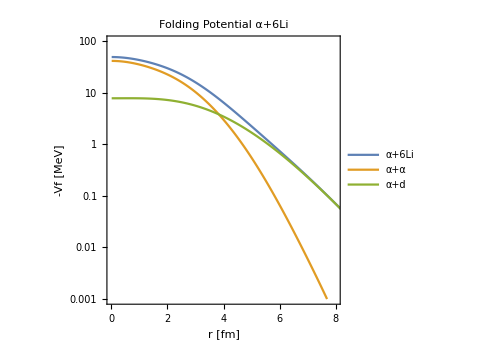

```mathematica
ListLogPlot[{Abs[totDensity],Abs[dda],Abs[ddn]},Joined->True,PlotRange->{{0,8},{0.001,100}},Frame->True,FrameLabel->{"r [fm]","-Vf [MeV]"},AspectRatio->1,ImageSize->Medium,PlotLabel->"Folding Potential α+6Li",PlotLegends->{"α+6Li","α+α","α+d"}]
```

```mathematica
dda⟦All,2⟧+ddn⟦All,2⟧;
f77Eform[#,4,4]&/@%;
fold=Transpose[{%, %}];
```

```mathematica
Export["fort.4",fold,"Table","FieldSeparators"->"\t"]
```

fort.4

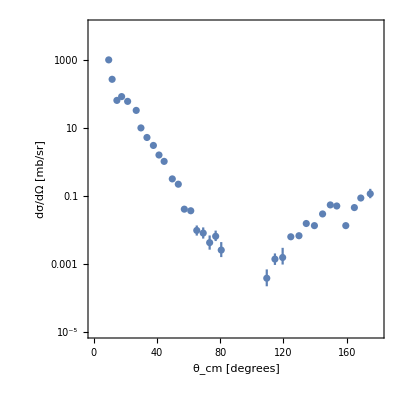

```mathematica
expPlot=ErrorListLogPlot[
{
{{#⟦1⟧,#⟦2⟧},ErrorBar[0,{#⟦3⟧,#⟦4⟧}]}&/@expScatData
},
ImageSize->400,
Frame->True,Axes->False,
AspectRatio->1,
PlotRange->{{0,180},{10^-5,10^4}},FrameLabel->{"θ_cm [degrees]","dσ/dΩ [mb/sr]"}
]
```

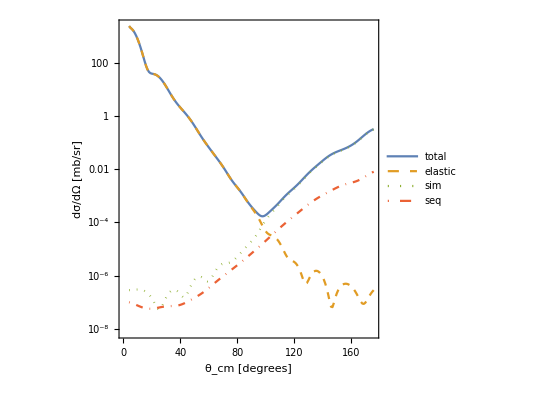

```mathematica
csPlot=ListLogPlot[{cs0,cs1,cs2,cs3},Joined->True,Frame->True,FrameLabel->{"θ_cm [degrees]","dσ/dΩ [mb/sr]"},AspectRatio->1,PlotRange->Full,PlotStyle->{Line,Dashed,Dotted,DotDashed},PlotLegends->{"total","elastic","sim","seq"}]
```

```mathematica
Show[csPlot,expPlot]
Export["cs.pdf",%,"PDF"]
```

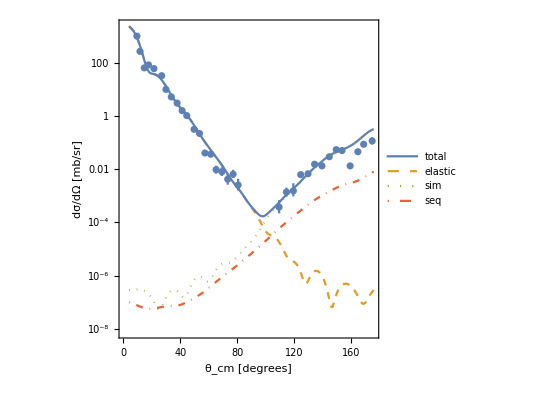

cs.pdf

## Plotting Data 9Be

```mathematica
totDensity1=Transpose[{be0⟦All,1⟧,be0⟦All,2⟧+be1⟦All,2⟧}];
```

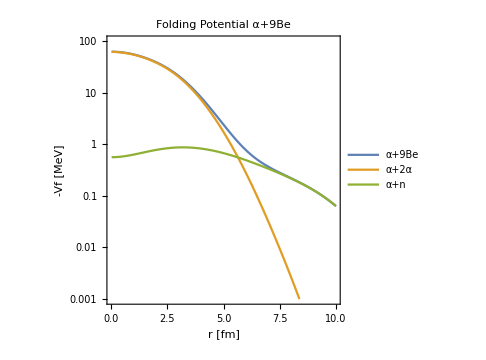

```mathematica
ListLogPlot[{Abs[totDensity1],Abs[be0],Abs[be1]},Joined->True,PlotRange->{{0,10},{0.001,100}},Frame->True,FrameLabel->{"r [fm]","-Vf [MeV]"},AspectRatio->1,ImageSize->Medium,PlotLabel->"Folding Potential α+9Be",PlotLegends->{"α+9Be","α+2α","α+n"}]
```